Università di Padova.   Corso di Laurea in Matematica.    Notebooks per il corso di Laboratorio Computazionale, a.a. 2021-2022

# Elenco progetti d’esame proposti

Questa è la lista dei progetti di esame proposti, con una breve descrizione del (possibile) lavoro da fare.
Per ulteriori informazioni, dubbi, problemi, valutazioni su cosa e come fare, etc, potete contattare il docente.
Buon lavoro!

## 1. Iterated Function Systems

Un esempio di IFS incontrato nel corso è stato il “gioco del caos” (vedere il notebook delle lezioni 11-12). Matematicamente si tratta dell’esistenza di un attrattore compatto per le iterazioni (anche in ordine random) di una famiglia di contrazioni. 

Un’ottima introduzione matematica si trova nel capitolo Iterated Function Systems di M. Barnsley nel libro Chaos and Fractals. The Mathematics Behind the Computer Graphics , edito da R.L. Devaney e L. Keen (AMS, 1989).

(Per una prima introduzione (non tanto buona, in realtà) all’argomento si può guardare la pagina “Iterated Function Systems” su Wikipedia. Informazioni più estese (ma forse un po’ sfuocate, come nello stile di quel libro, peraltro ricchissimo di informazioni e spunti) si trovano nei capitoli 5-8, ma soprattutto i primi due, del (notissimo) libro Chaos and Fractals. New Frontiers in Science di H.O. Peitgen, H.Jurgens, D. Saupe (Springer, 2004).)

Il progetto richiede di capire la teoria (al solito livello, senza dimostrazioni etc, ma matematicamente chiara) e illustrarla producendo alcune interessanti figure di attrattori, magari confrontando diversi modi di fare le iterazioni (random, ...)

Possibili attività:
- creazione di frattali classici via IFS
- creazione di forme naturali (le foglie di felce sono un classico)

Esempi di foglie di felce create con IFS da internet:

```mathematica
-Graphics- -Graphics--Graphics-
```

#### Esempi creati da studenti di Laboratorio Computazionale

“Foglia di acero” e di “viale alberato” (M. Moresco e M. Zocco, 2014):

```mathematica
-Graphics-                          -Graphics-
```

“Citta`” (G. Galante e C. Paoli, 2018):

## 2. Mandelbrot

Si sa molto (ma non ancora tutto) sulla struttura topologico-dinamica dell’insieme di Mandelbrot. Un ottimo (seppure un po’ difficile) punto di partenza è il capitolo The Mandelbrot set di B. Branner nel libro Chaos and Fractals. The Mathematics Behind the Computer Graphics , edito da R.L. Devaney e L. Keen (AMS, 1989).

Partendo da qui si possono cercare di capire, indagare numericamente ed illustrare un certo numero di aspetti dell’insieme di Mandelbort. Per esempio:
- Le componenti “iperboliche” e la loro relazione con orbite periodiche attrattive, già vista un po’ a lezione.
- La dinamica su J_0. 
- Il “potenziale” e il significato degli aloni che si osservano nelle figure.
- La relazione fra insieme di Mandelbrot e insiemi di Julia. I “punti di Misiurewicz” e i “dendriti”.
- I “raggi” e il problema della connessione locale. 
- L’insieme di Mandelbrot sulla sfera di Riemann.
- L’universalità dell’insieme di Mandelbrot. 
- Etc. 

Una fonte di informazioni molto dettagliate (ma un po’ diluite, come nello stile di quel libro, peraltro ricchissimo di informazioni e spunti) si trovano nel (notissimo e già citato) libro Chaos and Fractals. New Frontiers in Science di H.O. Peitgen, H.Jurgens, D. Saupe (Springer, 2004).

## 3. Geometrie non euclidee: disco di Poincaré e geometrie iperboliche ed ellittiche

Le geometrie non-euclidee differiscono da quella euclidea per il V postulato di Euclide (dati un punto P ed una retta r che non contiene P esiste una ed una sola retta r_P passante per P e parallela ad r.
- In una geometria ellittica questo assioma è sostituito dall’ipotesi che non esista alcuna r_P
- In una geometria iperbolica questo assioma è sostituito dall’ipotesi che esistano infinite r_P

In questo progetto si chiede di studiare modelli di geometrie iperboliche ed ellittiche.

### Disco di Poincaré

Il disco di Poincaré è un modello di geometria iperbolica. 
È costituito dal disco unitario in R^2= C
Le “rette” (geodetiche) sono:
- i diametri del disco
- gli archi di cerchio che intersecano ortogonalmente la frontiera del disco

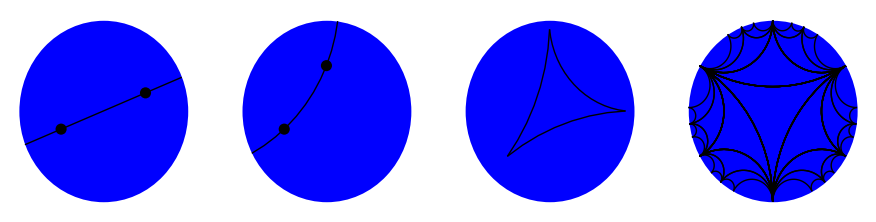

Una geodetica-diametro è univocamente determinata da uno dei suoi due estremi α = a+i b 
Una geodetica-arco di cerchio è univocamente determinata dal suo centro α = a+i b

La distanza che produce queste geodetiche è
   d(z_1,z_2) = arctanh|(z_2-z_1)/(1-z_1^*z_2)|
ed è prodotta dalla metrica Riemanniana (scritta in R^2)
   (1-x^2-y^2)^-2(dx ⊗dx+dy⊗dy)

#### Cosa fare?

Si possono fare alcune delle seguenti cose :

1. Scrivere un programma che disegni la geodetica fra due punti, un triangolo dati i tre vertici, etc.
Si possono far muovere i punti per mezzo di un locator.

2. Vale il teorema di Pitagora? E quanto è la somma degli angoli interni ad un triangolo?
(L'angolo fra due geodetiche è definito come l'angolo fra le tangenti ad essa)

Notazione:  D sta per disco di Poincarè; d sta per disco (disco di Poincarè)

Lemma che ci servirà per dimostrare il teorema di pitagora
	
	Lemma “dell’origine”: A un punto di D diverso dall’origine O. Allora esiste una d-retta l tale che la riflessione iperbolica in l mappa A in O.

	Teorema 2.1 La somma degli angoli interni di un triangolo iperbolico è < π .
	Dimostrazione . Grazie al "lemma dell' origine" possiamo mappare il d - triangolo ABC nel d - triangolo OB' C' tramite una trasformazione iperbolica che manda A nell' origine O . Siccome una trasformazione iperbolica preserva gli angoli, le somme degli angoli dei due d-triangoli sono le stesse . OB' e OC' sono delle rette euclidee, e B'C' fa parte di cerchio euclideo che 'si piega verso' l'origine. Così gli angoli a B' e C' del d-traingolo OB'C' sono minori degli angoli del traiangolo euclideo corrispondente OB'C', e gli angoli in entrambi i triangoli centrati in O sono gli stessi. Siccome la somma degli angoli del triangolo euclideo OB'C' è π, segue che la somma degli angoli del d-triangolo OB'C' è strettamente minore di π. _ 
                 
	Teorema 2.2 Preso un d-triangolo ABC  nel quale l’angolo in C è retto.Se a,b,c sono le lunghezze iperboliche di BC,CA,AB, allora  cosh 2 c = cosh 2 a * cosh 2 b . 
	DIMOSTRAZIONE : Usando il lemma dell' origine (?) possiamo assumere che C sia al centro del disco unitario, il punto A è al punto a' sul diametro orizzontale e il punto B è a ib' sul diametro verticale, dove a' e b' sono reali e positivi. 
Dalla formula della distanza segue che a = arctanh (b')  e  b = arctanh (a') . 
Ora mappiamo D in sè stesso tramite la trasformazione iperbolica M (z) = (z-a')/(1-z*a'). Sotto M, A va nell’orgine (che chiameremo d’ora in poi A’), B va nel punto B’, con coordinate complesse b''=(ib'-a')/(1-ia'b'), e C va nel punto C’ con coordinate -a’.
Siccome la trasformazione iperbolica preserva le lunghezze, la lunghezza iperbolica c di AB è equivalente alla lunghezza iperbolica di A’B’.
Per trovare c, la lunghezza iperbolica di AB, troviamo prima il modulo di b’’. 
   |b''|^2 = (|ιb' -a'|^2)/(|1-ιa'b'|^2)=((a')^2+(b')^2)/(1+(a')^2(b')^2).
   (N.B. cosh[2*arctanh[x']]=(1+(x')^2)/(1-(x')^2) )
   Usando questa formula e le osservazioni iniziali osserviamo che
  cosh[2a] = cosh[2*arctanh[b']]=(1+(b')^2)/(1-(b')^2)  
  cosh[2b] = cosh[2*arctanh[a']]=(1+(a')^2)/(1-(a')^2) 
  e siccome c = arctanh[|(b'')^2|] abbiamo che cosh[2c] = cosh[2*arctanh[b'']]=(1+(|b''|)^2)/(1-(|b''|)^2) 
  Da qui segue che 
cosh[2c] = (1+(|b''|)^2)/(1-(|b''|)^2) 
=(1+((a')^2+(b')^2)/(1+(a')^2(b')^2))/(1-((a')^2+(b')^2)/(1+(a')^2(b')^2))
= (1 + (a')^2 + (b')^2 + (a')^2 (b')^2)/(1 - (a')^2 - (b')^2 + (a')^2 (b')^2)
=(1+(b')^2)/(1-(b')^2)×(1+(a')^2)/(1-(a')^2) 
=cosh[2*arctanh[b’]] × cosh[2*arctanh[a’]]
= cosh[2a]×cosh[2b] __

3. Illustrare la non validità del postulato delle parallele con dei disegni

4. Quale è la forma di un cerchio (definite come l’insieme dei punti che hanno distanza d costante da un punto dato)?

Diamo due definizioni (punto medio e trasformazione iperbolica) che ci serviranno più avanti.

DEF: Un punto m è il punto medio iperbolico del segmento iperbolico che unisce a e b se m giace su questo segmento e vale d(a,m) = d(m,b) = 1/2d(a,b)

DEF: Una trasformazione iperbolica M è scritta nella forma M(z)=K(z-m)/(1-m̄ z) (chiamata forma canonica) dove K e m sono numeri complessi con |K| = 1 e m∈D.

 
Il cerchio iperbolico con raggio iperbolico r e centro iperbolico c è l’insieme definito da {z : d(c,z) = r, z ∈ D}.
Un cerchio iperbolico assomiglia graficamente a un cerchio euclideo?
CASO c=0: Nel caso di un cerchio iperbolico di raggio ip r centrato nell’origine, l’insieme di definizione è dato da {z : d(0,z) = r, z ∈ D} = {z : arctanh(|z|) = r, z ∈ D} = {z : |z| = tanh(r), z ∈ D}. Questo è un cerchio euclideo con raggio tanh(r) centrato nell’origine.
CASO GENERALE
	Teorema: Ogni cerchio iperbolico è un cerchio euclideo in D, e viceversa.
	Dimostrazione: Caso in cui è centrato nell’origine già dimostrato.
C un cerchio iperbolico con centro m ≠ 0.  Il diametro di D passa per m e incontra C nei punti a e b, K è il cerchio euclideo con diametro ab e centro p. Faremo vedere che C è un cerchio euclideo facendo vedere che esso coincide con K. Per far questo prendiamo M la trasformazione iperbolica definita così M(z) = (z-m)/(1-m̄ z) con z∈D e prendiamo a’ e b’ come immagini di a e b rispettivamente sotto M. 
M preserva le distanze iperboliche e mappa m in O ⇒ M mappa C in un cerchio iperbolico C’ con centro O. Ma sappiamo già che un tale cerchio è anche un cerchio euclideo. Inoltre, siccome il segmento ab passa in m, la sua immagine a’b’ passa in O ed è quindi il diametro di C’. 
M preserva gli angoli e siccome ab incontra K con angoli retti ⇒ M mappa K in un cerchio K’ il quale incontra a’b’ con angoli retti nei punti a’ e b’ ⇒ a’b’ è anche il diametro di K’ ⇒ C’ coincide con K’ e quindi C coincide con K.
Viceversa, K è un cerchio euclideo qualunque con centro p ≠ 0 e il diametro di D per p incontra K nei punti a e b. Se C è il cerchio ipercbolico per a e b con centro iperbolico il punto medio iperbolico m di ab, possiamo usare gli stessi argomenti usati prima per dedurre che K coincide con C. Si conclude che K è un cerchio iperbolico.__

5. Le riflessioni attoro alle geodetiche, nel disco iperbolico, sono date dalle seguenti formule:
- riflessione attorno alla geodetica-diametro determinata da α=a+i b:
    z → α^2 z^* 
- riflessione attorno alla geodetica-cerchio determinata da α=a+i b:
    z → (α z^*-1)/(z^*-α^*)
Investigare l'esistenza di tassellazioni del disco iperbolico costruite riflettendo iterativamente un triangolo attorno ai suoi tre lati.
Per esempio, si può partire
- con un triangolo equilatero con i vertici sul bordo del disco 
- con un triangolo con un vertice nell'origine, l'angolo nell'origine = π/7 e i due angoli opposti = π/3 e π/2, 
   rispettivamente. 

6. Scrivere le equazioni (di Lagrange) delle geodetiche e integrarle (numericamente? analiticamente?)

7. Qualunque altra cosa vi sembri interessante!

#### Formule utili

Per disegnare gli archi di geodetica-cerchi si può usare la primitiva grafica Circle. Serve una funzione che calcola l'angolo fra due punti. Per esempio si può usare:

```mathematica
angolo[{x1_,y1_},{x2_,y2_}]:=Module[{  },
a1=ArcTan[x1,y1]//N;a2=ArcTan[x2,y2]//N;
        If[Abs[a2-a1] ≤ Pi,Sort[{a1,a2}],Sort[Mod[{a1,a2},2Pi]]]]
```

```mathematica
Show[Graphics[{Circle[{0,0},1],Point[a], Point[{0.5,0.5}],Point[{0,1}]}]]
```

Attenzione: assicurarsi sempre che gli argomenti di     Sort   siano numeri  interi, razionali, o reali approssimati. Confrontare gli output dei seguenti comandi:

Sort[{Pi,10}]
 
Sort[{Pi,10}//N]

e, tanto per capire che non è un bug,

Sort[{Pi,10},Smaller]

Il centro della geodetica-cerchio passante per due punti P1 e P2 (di R^2) si calcola così: Inverse[{P1,P2}].{1+P1.P1,1+P2.P2}/2

### Superfici immerse in R^3 con geometria non-euclidea

Esempio di geometrie ellittiche ed iperboliche si incontrano su superfici immerse in R^3. Per esempio, la restrizione della metrica euclidea
- a una sfera produce una geometria ellittica
- alla pseudosfera di Beltrami produce una geometria iperbolica
In entrambi i casi le “rette” sono le geodetiche della superficie.

Le equazioni delle geodetiche sono note. Volendo si possono anche creare le geodetiche come soluzioni delle equazioni di Lagrange di un’opportuna Lagrangiana (quale?).

Si possono investigare questioni analoghe a quelle della sezione “Cosa fare?” in uno o più di questi modelli. In particolare: quanto vale la somma degli angoli interni di un triangolo?

Se siete interessati potete contattare i docenti.

### Bibliografia

D.A. Brannan, M.F. Esplen e J.J. Gray, Geometry (Cambridge University Press, 1999) 
R. Harshorne, Geometry: Euclid and Beyond (Springer, 1997).
R. Courant e H. Robbins, Che cos’è la matematica? (Einaudi, 1950)

## 4. Pendolo “magnetico”

È il sistema illustrato a lezione e descritto nella sezione 3.2.B  di “F. Fassò, Primo sguardo ai sistemi dinamici. A.A. 2015-2016 (CLEUP)”. Lo scopo base del progetto è quello di produrre una figura del tipo di quella là mostrata a pagina 53, di metterne in evidenza i dettagli con successivi zoom, e di tracciare traiettorie del pendolo (magari interattivamente).

Volendo, si può fare un’analisi più dettagliata di equilibri e loro stabilità al variare dei parametri.

Un’ottima descrizione del problema si trova nei capitoli 1-3 della tesi di laurea “Bacini di attrazione frattali nella dinamica di un pendolo caotico” di M. Gorghetto, che si trova fra le tesi di laurea sulla pagina web di F. Fasso`. (Il capitolo 2 è solo in parte rilevante).

Se c’è qualcuno interessato ci contatti e ne parliamo meglio.

## 5. Pendolo doppio

Questo progetto è più indefinito degli altri, e potra` essere meglio precisato durante l’ultima lezione.

Lo scopo è quello di indagare la dinamica caotica del pendolo doppio. Le tecniche da usare sono tipiche dello studio numerico di equazioni differenziali (sezioni di Poincaré, che verranno introdotte nell’ultima lezione). 

L’analisi va fatta costruendo numericamente una sezione di Poincaré a diversi (significativi) valori dell’energia. Nel sistema vi sono 4 orbite speciali che, in ordine di energia crescente, sono: l’equilibrio inferiore (punto di minimo dell’energia, ellittico), i due equilibri `intermedi’ (un pendolo sù e uno giù, con le loro varietà stabile ed instabile unidimensionali, l’equilibrio superiore (i due pendoli in sù, con le sue varietà stabile ed instabile bidimensionali). Inoltre, i modi normali di oscillazione attorno all’equilibrio “giù-giù” approssimano delle orbite periodiche del sistema. L’analisi sulle sezioni di Poincaré deve identificare i corrispondenti punti fissi della mappa di Poincaré con le loro varietà stabili ed instabili, quando presenti. 

Se c’è qualcuno interessato ci contatti e ne parliamo meglio.

## 6. Mappa logistica

Le iterazioni della mappa logistica
       f_μ(x)= μ x (1-x)
che dipende dal parametro positivo μ costituiscono (a prima vista) una versione discreta della dinamica continua descritta dall’equazione logistica. A differenza di quest’ultima, però, la dinamica discreta della mappa logistica è enormemente complicata. 

Un’introduzione (seppure un po’ difficile) si trova nel capitolo Dynamics of simple maps di R. Devaney nel libro Chaos and Fractals. The Mathematics Behind the Computer Graphics , edito da R.L. Devaney e L. Keen (AMS, 1989).

Qui spiego un po’ delle cose che si potrebbero fare. Se siete interessati, magari ne discutiamo per definire meglio il lavoro.

### a. Metodo grafico per la determinazione delle orbite

Come visto a lezione c'è un metodo grafico molto semplice, e utile, che permette di tracciare le orbite di una qualunque mappa f :R→R.
Si comincia col tracciare il grafico di f e la bisettrice del I e III quadrante.
L'evoluto  f(x)  di un punto  x  si determina poi così:
- si segna il punto di coordinata  x sull'asse delle ascisse:   ( x , 0 ).
- si traccia il segmento verticale che lo congiunge con il grafo di  f , arrivando in ( x , f(x) )
- si traccia il segmento orizzontale che congiunge (x,f(x)) con la bisettrice, arrivando in ( f(x) , f(x) )
- si  traccia il segmento verticale che congiunge quest'ultimo punto con l'asse delle ascisse, arrivando in ( f(x) , 0 ).

Per evitare di tracciare troppi segmenti, può essere conveniente segnare i punti non sull'asse delle ascisse, ma sulla bisettrice:

(La figura mostra le prime 5 iterazioni; il punto blu e` l'ultimo)

Si noti che i punti fissi corrispondono alle intersezioni fra il grafico e la bisettrice.

Possibile attività: Potete scrivere una funzione che produce il grafico delle iterazioni di f_μ, trattando μ, il punto iniziale il numero di iterazioni come variabili.

### b. Primo sguardo alla mappa logistica

Proposizione: 
1. Per ogni μ>0, f_μ ha i due punti fissi  0 e x_μ=1-1/μ. 
2. Per ogni μ>0, se  x_0< 0  oppure  x_0 > 1 allora    f_μ^n(x_0)→ ∞

Dim: 1. Ovvio.
2. La dimostrazione formale (facile) è lasciata come esercizio. Ci si convince peraltro della verità dell'affermazione facendo uso del metodo grafico:

Dunque, la dinamica “interessante” della mappa logistica ha luogo nell'intervallo [0,1]. Per questo, ci interessiamo solo ad orbite che restano al suo interno. (Qui, “interessante” si riferisce non solo all'applicazione ecologica, per la quale 0<x<1, ma anche agli aspetti matematici: se qualcosa di interessante avviene, avviene  in questo intervallo).

Proposizione:
1) Se 0 < μ ≤ 4 allora tutte le orbite con dato iniziale in [0,1] vi restano.
2) Se μ > 4 allora vi è un intervallo A_0 ⊂ [0,1] tutti i punti del quale scappano da [0,1] alla prima iterazione.

Dim: 
1) Basta osservare che  0 <f_μ(x)=μx(1-x)<1 per 0<x<1.
2) Se μ > 4, il massimo di  f_μ(x)  è > 1 e dunque esiste un intervallo A_0 ⊂ [0,1] e simmetrico rispetto ad 1/2, nel quale f_μ(x) > 1.

Vi sono dunque (almeno) due diversi regimi, a seconda che μ≤4 o μ>4.

### c. La mappa logistica per 0 < μ ≤ 4

#### c.1. Diagramma di biforcazione

A questo punto può essere utile sperimentare un po' sulla dinamica. Per 0<μ<4 e nell’intervallo [0,1] si osserverà quanto segue:

- Per 0<μ<1 tutte le orbite tendono asintoticamente al punto fisso 0.
- Per μ≥1 ma piccoli, diciamo  μ ≤ μ_1 con qualche μ_1>1, tutte le orbite (con dato iniziale in [0,1]) tendono al punto fisso x_μ.
- Per μ più grande, ma non troppo, diciamo μ_1< μ < μ_2, tutte le orbite tendono ad un'orbita periodica di periodo 2;   i due punti di quest'orbita “emanano” dal punto fisso e si allontanano l'uno dall'altro al crescere di μ.
- Per μ ancora più grande, ma non troppo, diciamo μ_2< μ < μ_3, tutte le orbite tendono ad un'orbita periodica di periodo 4.
- Poi, in un intervallo molto piccolo μ_3< μ < μ_4, tutte le orbite tendono ad un'orbita periodica di periodo 8
- Al crescere di μ la dinamica diventa più complicata. Se μ si avvicina a un valore μ_∞ un po' minore di 4, o
   lo supera, le orbite non sembrano più asintotiche ad orbite periodiche (di periodo non troppo alto).

NB: Se μ > 4, naturalmente, come già sappiamo, vi sono punti iniziali interni a [0,1] le cui orbite tendono a -∞: nei conti si incontrano problemi di overflow.

Per μ < μ_∞, la dinamica sembra dunque essere dominata da un'orbita periodica che attrae tutte le altre obite. Il periodo di quest'orbita periodica dipende da μ e, a certi valori di μ, raddoppia. Vi è una successone di (infinite) biforcazioni, con raddoppiamento del periodo.

#### c.2. Diagramma di biforcazione

Una chiave di lettura dei risultati dell’analisi sperimentale si ottiene con lo studio teorico dei primi passi della successione di biforcazioni.

Ricordiamo che un punto fisso p di una mappa f:R→R è attrattivo se |f’(p)| < 1 e repulsivo se |f’(p)| > 1.  La attrattività/repulsività di un'orbita periodica si definisce e si studia in modo analogo, riguardandola come un punto fisso di una potenza della mappa.

Esercizi (analitici: volendo si può usare Mathematica) 
(1) Mostrare che il punto fisso  0 della mappa logistica è repulsivo per tutti i μ>1
(2) Mostrare che il punto fisso  p_μ = 1-1/μ della mappa logistica è attrattivo se 1<μ<3 e repulsivo per μ>3, e che 0 è repulsivo per tutti i μ>1
(3) Mostrare che l'orbita di periodo minimo 2 della mappa logistica esiste per μ>3 ed è attrattiva per 3<μ<1+√6.

Dunque, μ_1=3 e μ_2=1+√6=3.449...

Osservazione Applicando la Proposizione si può dimostrare che un punto fisso attrattivo, o un'orbita periodica attrattiva, attrae tutte le orbite in un certo intervallo, non che le attragga (quasi) tutte, come i calcoli numerici sembrerebbero a prima vista suggerire. In effetti, con più lavoro, si puo` dimostrare, nel caso della mappa logistica con μ<4, questo fatto più forte.

Diagramma di biforcazione relativo a queste prime due biforcazioni:

Possibile attività: Proseguire il diagramma a qualche altra biforcazione. 
(Vedere anche piu` sotto)

#### c.3. Meccanismo che produce le biforcazioni

Per capire il meccanismo che produce la nascita delle due nuove orbite periodiche, ed il trasferimento ad esse dell'attrattività, bisogna pensare ad esse come punti fissi di f_μ^2. Per determinare i punti fissi di f_μ^2 bisogna tracciarne il grafico.  Questo si fa, qualitativamente, a partire dal grafico di f_μ, tenendo presente che f_μ^2=f_μ o f_μ . Si osservi che
• f_μ^2 assume il valore x_μ nei due punti f_μ^-1(x_μ) , cioè x_μ ed x'_μ=1/μ<x_μ.
• Poiche f_μ mappa biunivocamente l'intervallo (0,x'_μ) nell'intervallo (0,x_μ), il grafico di f_μ^2 nell'intervallo (0,x'_μ) è qualitativamente simile a quello di f_μin (0,x_μ) ed in particolare ha ivi un (unico) massimo. (Il grafico di f_μ^2 nell'intervallo (0,x'_μ) si ottiene “comprimendo” quello di f_μin (0,x_μ). 
• La stessa cosa avviene nell'intervallo (x_μ,1), eccetto che, essendo ivi f_μ decrescente, il grafico di f_μ^2 risulta ivi una copia compressa e speculare di quello di f_μ in (0,x_μ).
• Infine, poiché f_μ mappa biunivocamente l'intervallo (x'_μ,1/2) nell' intervallo (x_μ,μ/4), con x_μ<μ/4<1, nel quale f_μ è decrescente, f_μ^2 mappa tale intervallo nell'intervallo (x_μ,f_μ(μ/4)) ed è ivi decrescente.
• Per simmetria, f_μ^2 mappa l'intervallo (1/2,x'_μ) nell'intervallo (f_μ(μ/4),x_μ), ed è ivi crescente. Dunque, f_μ^2 ha un minimo in 1/2. (Poiche` f_μ^2 è un polinomio, il raccordo nel minimo deve essere liscio).

Quale è il meccanismo che produce la nascita dei due nuovi equilibri, ed il trasferimento di attrattività ad essi?
I due fatti sono collegati:
- Quando μ passa per 3, la derivata di f_μ(x_μ)  passa per 1(crescendo) e dunque il grafico di f_μ  (in rosso nelle figure) diventi tangente alla bisettrice.
- Questo fa perdere attrattività ad x_μ, e fa anche sì che il grafico di f_μ  intersechi la bisettrice nel solo punto x_μ per μ≤3, in x_μ ed in altri due punti per μ>3.
- Inizialmente, per μ vicino a 3, il valore assoluto della derivata di f_μ nei due nuovi punti fissi è <1.

#### c.4. Cascata di biforcazioni

Una volta capito il meccanismo alla base della prima biforcazione con raddoppiamento del periodo, si capisce che questo processo si ripete.
In effetti, al crescere di μ, la pendenza del grafico di f_μ^2 nei due punti fissi attrattivi cresce fino a che il valore assoluto della derivata passa per 1. A tal punto, essi divengono instabili e ciascuno di essi biforca in due punti fissi di f_μ^4, cioè orbite periodiche di f_μ^2 di periodo doppio.

Si potrebbe ripetere tutta l'analisi fatta per il caso di periodo 2. I polinomi sono di grado troppo alto per essere risolti, ma numericamente ce la si fa.
(L'analisi numerica è soprattutto complicata dal fatto che ci sono 8 orbite di periodo 4 che compaiono a circa 3.95,e che devono dunque essere ignorate nell'analisi della biforcazione a 3.449....)

Avviene che questo processo va avanti infinite volte per μ<μ_∞<4.
Per studiarlo si può procedere numericamente, sfruttando il fatto che (anche se non lo abbiamo discusso) avviene che, per ogni μ<μ_∞, quasi tutte le orbite sono attratte da un'orbita periodica.

Possibile attività: Tracciare il diagramma di biforcazione sfruttando il fatto che, assunto che quasi tutte le orbite siano attratte da un'orbita periodica, è sufficiente seguire l'evoluzione di un'orbita scelta a caso e (teoricamente a meno di essere molto sfortunati, cioè con probabilità zero, ma in pratica con certezza, a causa degli errori numerici) si vedrà l’orbita convergere verso l'orbita periodica attrattiva.

Suggerimenti pratici:
- Fare un grafico con μ in ascissa e i punti dell'orbita in ordinata.
- Prendere un numero sufficientemente grande di valori di μ, abbastanza grande da ottenere una figura chiara.
- Per ogni considerato valore di μ plottare una sola orbita, per esempio quella di x_0= .5 (che, come si potrebbe provare, converge sempre ad un'orbita periodica).
- Per visualizzare il comportamento asintotico dell'orbita (che è essenziale per vedere se essa converge o no ad un'orbita periodica) bisogna scartare i suoi primi punti. Si può per esempio provare a fare 1000 iterazioni e tenere solo le ultime 100.
- Il disegno viene più chiaro se si disegnano punti piccoli
- Non superare il valore μ=4, se no l'orbita tende a -∞ e si va in overflow
- Il numero di valori di μ può andare da alcune centinaia ad alcune migliaia, a seconda di quel che si vuole ottenere.

Sul diagramma di biforcazione si distinguono con chiarezza le prime biforcazioni. Con un po' di cura, zoomando sui dettagli, si riesce in realtà a evidenziarne parecchie.

L'indicazione chiara del diagramma di biforcazione prodotto numericamente è che la successione μ_1, μ_2, μ_3, ...... converge ad un limite μ_∞<4. 
Oltre questo limite, la dinamica diventa più complicata: si alternano delle bande nelle quali la dinamica non sembra asintotitca ad un'orbita periodica e  “finestre” nelle quali si osservano cascate di biforcazioni per raddoppiamento del periodo, a partire da orbite periodiche di varii periodi (per es., è molto ben visibile quella di periodo 3).

Possibile attività: Evidenziare la struttura del diagramma di biforcazione su diverse scale, facendo degli ingrandimenti successivi che seguono biforcazioni successive. Si osserva un qualche tipo di autosimilarità? Per esempio, la cascata di biforcazioni di una delle orbite di periodo 3 assomiglia a quella completa?

### d. Costante di Feigenbaum. Universalità

Sia μ_n il valore di μ al quale si verifica la n-ma biforcazione. È un fatto che la successione delle distanze fra le biforcazioni è approssimativamente geometrica: per n grande, 
         (μ_(n+1)- μ_n)/(μ_n- μ_(n-1)) ∼  1/k
ove k è una costante positiva, chiamata costante di Feigenbaum.

Possibili attività:
- Provare a determinare la costante k determinando i primi (sei, sette, o quel che riuscite) valori della successione μ_1, μ_2, μ_3, ...... 
- Stimare μ_∞ assumendo una crescita geometrica e confrontarlo con il diagramma di biforcazione.
- Alla biforcazione n, ogni punto fisso di f^(2^n) biforca producendo due punti fissi di f^(2^(n+1)); al crescere di μ, la distanza fra questi due punti fissi aumenta. Sia d(n+1) la loro distanza quando essi biforcano. Si riesce a stabilire l’asintotica di d(n+1)/d(n) ?

Osservazione: si puó automatizzare la ricerca della biforcazione.
Per determinare la biforcazione n-esima si parte da un appropriato valore di μ inferiore a quello di boforcazione (stimato ad occhio) e si confrontano, per un opportunamente grande N, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi siamo arrivati alla biforcazione.

La crescita gometrica dei valori di biforcazione non è peculiare della mappa logistica. Lo scenario di raddoppiamento del periodo visto qui si presenta tale e quale per ogni mappa f dell'intervallo [0,1] su se stesso che abbia un unico massimo, sia ovunque nonnegativa e sia nulla agli estremi dell'intervallo. Che questo succeda, si capisce facilmente ripercorrendo tutta l'analisi fatta per la mappa logistica. Più sorprendente è che questa “universalità” sia anche quantitativa: la costante k che determina l'asintiotica della successione geometrica delle lunghezze degli intervalli fra le biforcazioni è la stessa per tutte queste mappe! Questo fatto è noto come congettura di Feigenbaum (la sua dimostrazione, dovuta a Landford, è stata una delle prime computer-assisted proofs).

Possibile attività: Controllare l'universalità della costante di Feigenbaum su un'altra mappa, diversa da quella logistica.

### e. μ>μ_∞: Dinamica caotica (separazione geometrica orbite)

Si puòmostrare che, se μ>4, le orbite che non scappano dall'interno dell'intervallo [0,1] restano su un insieme invariante che ha la struttura di un Cantor ternario. (Si usa in modo essenziale il fatto che la mappa assume valori >1). È molto difficile studiarlo numericamente perché, appunto, tutte le altre orbite prima o poi scappano. 
La stessa cosa avviene per μ_∞ < μ ≤ 4 (eccetto naturalmente nelle “finestre” regolari nelle quali si hanno cascate di raddoppiamento del periodo).

In entrambi i casi, la dinamica è “caotica”. Non diamo una definizione precisa di questo fatto, ma ci limitiamo a mettere in evidenza un aspetto fondamentale della “caoticità”: la dipendenza sensibile dai dati iniziali.

Una semplice stima mostra che le orbite di una mappa f  si allontano l'una dall'altra al più geometricamente in fretta:
       |f^n(x)-f^n(y)| < A^n |x_0- y_0|
per qualche costante positiva A.  (Infatti |f(x) - f(y)| < sup_z |f’(z)| |x-y|  e poi induzione).

Naturalmente, questa è una stima e in casi particolari la separazione fra le orbite potrebbe essere molto più lenta. Anzi, le orbite potrebbero restare a distanza costante o addirittura avicinarsi l'un l'altra. Quest'ultimo caso si verifica, naturalmente, se tutte le orbite tendono asintoticamente ad un punto fisso o ad un'orbita periodica.

In altri casi, però, la separazione fra orbite vicine può davvero essere geometrico, di ragione A>1, e questo pone dei limiti alla predicibilità dell'evoluzione: piccolissime variazioni nelle condizioni iniziali possono portare a evoluzioni completamente diverse: nonostante il determinismo della legge di evoluzione, in pratica il futuro è impredicibile.

Possibile attività: Provare a determinare la separazione fra orbite (molto!) vicine della mappa logistica. Per cominciare, si possono plottare le due orbite su uno stesso grafico, magari in colori diversi, e vedere come la loro separazione varia al variare della loro distanza iniziale. 
- Iterare la mappa poche volte (qualche decina o centinaia di volte, arrestandosi prima che la separazione si saturi - non puo` essere > 1!)
- Studiare qualche orbita per un valore di μ<μ_∞,  poi per un valore μ>μ_∞ in una banda caotica e, magari, anche per un valore μ>μ_∞ in una finestra regolare.
Si riesce a vedere qualcosa in modo chiaro?

Osservazione: Per migliorare la comprensione dei questo fatto, è necessario fare un grafico logaritmico (LogListPlot) della distanza fra le due orbite in funzione del numero di iterazioni. Cercare di produrre qualche grafico che metta bene in evidenza la differenza fra i due regimi.
NB: È importante il valore della separazione iniziale, purchè piccola, naturalmente?

Possibile attività: Invece di studiare la separazione di orbite vicine si può investigare come la dinamica espande i vettori tangenti, studiano la crescita di |f’| lungo un’orbita. Si vedano gli “esponenti di Lyapunov” nel notebook di una delle ultime lezioni del corso.

### f. Finestre regolari

È un fenomeno molto interessante. Al crescere del parametro, il “caos” non aumenta sempre. A volte, anzi, scompare. Questo è legato all'apparire di orbite periodiche attrattive, che stabilizzano la dinamica. Corrispondentemente, nel diagramma di biforcazione appare una finestra regolare, con un'orbita periodica, la quale poi biforca per raddoppiamento del periodo, ed una nuova cascata si mette in moto. La più grossa di queste finestre è quella di periodo 3.

Il teorema di Sarkovskii afferma che se una mappa continua di un intervallo in sé ha un' orbita periodica di un dato periodo allora contiene orbite periodiche di molti altri periodi. Precisamente, se esiste un’ orbita periodica di periodo N allora esistono tutte le orbite periodiche di periodo minimo “dominato” da N. 
La “dominazione” è il seguente ordinamento “→” degli interi positivi:
3 →  5 →  7 →  9 →  11 →  ...      →  3×2 →  5×2 →  7×2 → ...     → 3×2^2 →  5×2^2 → ...   →         ...   →    2^3 →  2^2 →  2 → 1

Notevole è il fatto che se il sistema contiene un' orbita di periodo  3 allora contiene orbite di tutti i periodi.

Possibile attività: illustrare il teorema di Sarkovskii sulla mappa logistica.